# Gradient Descent

Aaron Lopes

## Backstory

### Mathematical Motivation

```mathematica
WordDefinition["gradient"]
```

{the property possessed by a line or surface that departs from the horizontal,a graded change in the magnitude of some physical quantity or dimension}

In mathematics, the term gradient holds several definitions. Most generally, it is interchangeable with slope, describing the rate of change of a function. In multivariate and vector calculus, it describes the direction in which the steepest upward rate of change occurs within a function. This can be found by taking the derivative of the function with respect to (w.r.t) its independent variables.

```mathematica
{Slider[Dynamic[a],{-5,5}],Dynamic[a]}
```

{,}

```mathematica
{Slider[Dynamic[b],{-5,5}],Dynamic[b]}
```

{,}

The sliders above will allow you to change the horizontal and vertical steepness of the quadric surface below, also known as a hyperbolic paraboloid. The darker the hue, the more dramatic the ascent or descent.

```mathematica
g=.
```

```mathematica
g[a_,b_][x_,y_] := (x/a)^2-(y/b)^2
```

```mathematica
Dynamic[Plot3D[ g[a,b][x,y],{x,-5,5},{y,-5,5},ColorFunction->Hue]]
```

The computed gradient below will provide a vector which will point to the direction of steepest ascent on the hyperbolic paraboloid.

```mathematica
grad = Grad[g[a,b][x,y], {x,y}]
```

{0.42084 x,-2.46914 y}

We see that, depending on the chosen values for a and b, the plotted vectors point toward the direction of steepest ascent.

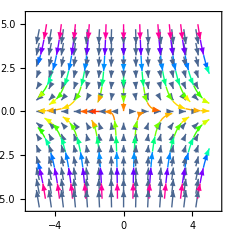

```mathematica
VectorPlot[grad, {x, -5, 5}, {y,-5,5},StreamPoints->Coarse, StreamColorFunction->Hue]
```

Conversely, the negative gradient represents the direction of steepest descent.

```mathematica
grad = -grad
```

{-0.42084 x,2.46914 y}

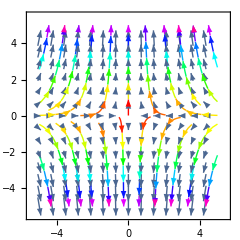

```mathematica
VectorPlot[(grad), {x,-5,5}, {y,-5,5},StreamPoints->Coarse, StreamColorFunction->Hue]
```

### Application to Machine Learning

The method of gradient descent as a minimizer for nonlinear functions was first introduced by the French mathematician Augustin-Louis Cauchy,

```mathematica
WebImageSearch["Augustin-Louis Cauchy", "Images"][[1]]
```

-Graphics-

whose work was motivated by the mechanics of astronomical bodies.

## Learning Example with Gradient Descent

Suppose we have a dataset which spans 6 years, which represents the number of people infected with Tuberculosis, starting in 2001 and going to 2006. We can see that our plotted data represents somewhat of an upwards trend, so our line of best fit should reflect this trend.

```mathematica
SeedRandom[]
```

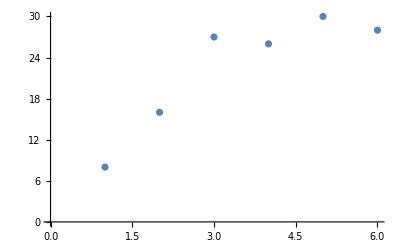

```mathematica
data ={{1,8},{2,16},{3,27},{4,26},{5,30},{6,28}};
ts = TimeSeries[data];
ListPlot[ts]
```

In order to build our regression model, we will first generate two random values, a and b, which will represent the slope of our line and the y-intercept, respectively. In order to properly structure of time-value matrix, we will transpose it to create two separate columns.

```mathematica
Clear[ypred,yp,sse,totalsse,grada,gradb,totalgrada,totalgradb,a,b]
```

```mathematica
xa = Transpose[data][[1]];
```

```mathematica
ya = Transpose[data][[2]];
weightsab = RandomReal[{1,5},{2}];
```

After looking at the plotted data, we can estimate that the slope of our line will be somewhere between 1 and 5, so we will generate random values in this range.

```mathematica
a = weightsab[[1]];
b= weightsab[[2]];
```

```mathematica
predict[a_, b_, x_] := a + b * x;
```

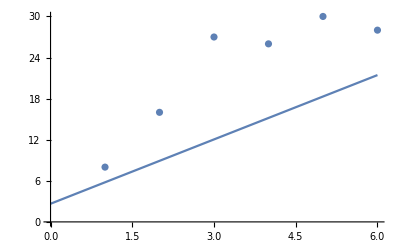

```mathematica
Show[ListPlot[ts],Plot[b+a*x,{x,0,6}]]
```

Comparing the line to our plotted data, we can see that the fit provided by this line is far from best, so we will introduce the concept of gradient descent to fine tune our parameters, a and b.

```mathematica
yp = predict[a,b,xa];
```

```mathematica
sse[yactual_, ypred_] := Total[1/2*(yactual-ypred)^2]
grada[yactual_, ypred_] := -(yactual-ypred);
gradb[yactual_,ypred_,xactual_] := -(yactual- ypred) * xactual;
```

```mathematica
sumsquarederror = sse[ya,yp]
```

386.824

```mathematica
totalgrada = Total[grada[ya,yp]]
```

-63.1844

```mathematica
totalgradb = Total[gradb[ya,yp,xa]]
```

-240.217

Update weights a and b using the calculated gradients. Step size will equal 0.01, we will attempt to reach

```mathematica
s[X_,Y_,a_,b_ ] := 1/2*(Y-(a+b*X))^2
```

```mathematica
Plot3D[s[x,y,a,b],{x,-5.0,5.0},{y,-5.0,5.0},ColorFunction->Hue]
```

-Graphics3D-

2.31546

5.34093

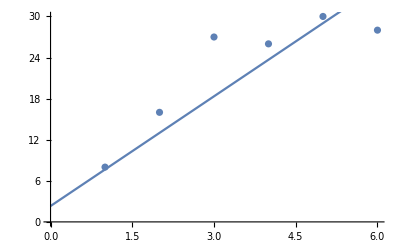

```mathematica
a= a - 0.01*totalgrada
b=b-0.01*totalgradb
Show[ListPlot[ts],Plot[a+b*x,{x,0,6}]]
```

```mathematica
yp = ypred[a,b,xa];
sumsquarederror = sse[ya,yp]
```

65.4847

## Training the Model